```mathematica
(* WALKING KINEMATICS: Segment angles and polar co-ordinates - Filtered, Archive data*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(*This code requires input of single trial at a time*)
(*TrialMatrix information
KM01_RUN_02 [1,1]
KM02_RUN_01[2,1], KM02_RUN_02[2,2], KM02_RUN_09[2,3]
KM04_RUN_09[3,1], KM04_RUN_11[3,2], KM04_RUN_12[3,3]
KM05_RUN_04[4,1], KM05_RUN_08[4,2]
KM06_RUN_11[5,1], KM06_RUN_12[5,2], KM06_RUN_13[5,3], KM06_RUN_15[5,4], KM06_RUN_16[5,5]
KM07_RUN_14[6,1], KM07_RUN_16[6,2], KM07_RUN_17[6,3]
KM08_RUN_09[7,1], KM08_RUN_10[7,2]
KM23_RUN_01[8,1], KM23_RUN_02[8,2], KM23_RUN_03[8,3], KM23_RUN_05[8,4]*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Determine operating system *)

os=$OperatingSystem;
frogworkpath="C:\\YOUR FILE DIRECTORY HERE\\" (*Set your main file directory, not to the folder where raw or archived data are stored*)
(*e.g. frogworkpath="C:\\Users\\Documents\\"*)
(*for Mac users change "C:\\" to "\\Volumes\\"*)

dataDirectory="YOUR DIRECTORY TO ARCHIVED .DAT DATA"; (*Set the directory where archived data from the "Code to Archive Data" notebook was exported to*)

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(***********************************************************************************)

(* Determine animal filename *)

Needs["GraphUtilities`"]
whatFrog[filename_]:=StringTake[filename,{3,4}](*extracts the animal number*)
trialFiles=FileNames[];
ntrials=Length[trialFiles];
trialMatrix=GatherBy[trialFiles,whatFrog];(*organize the trials in a matrix *)
ExpressionTreePlot[trialMatrix,VertexLabeling->Tooltip];

(******************************************************************************************)

(*INPUT - Type Animal Filename *)

animalfilename=trialMatrix[[8,4]] (*Change this to match trial matrix information above*)
(*e.g. animalfilename=trailMatrix[[8,4]] uses KM23_RUN_05*)

(******************************************************************************************)

(* Import raw data *)

allrawtrialdata=Import[animalfilename,"Data"];

(***********************************************************************************)

(* Import metadata*)
(*Set the directory where the METADATA.xlsx is saved*)

(*SET DIRECTORY*)
dataDirectory="YOUR DIRECTORY TO METADATA.xlsx FILE";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

importedmetadata=Import["METDADATA.xlsx","Data"];
metadata=importedmetadata[[1,2;;24,All]];

(***********************************************************************************)

(* Metadata file map: Locate information *)

filenamerow=Flatten[Position[metadata,animalfilename]][[1]];

SVL=metadata[[filenamerow,2]];
Framerate=metadata[[filenamerow,3]];
TotalNumberRawFramesDigitised=metadata[[filenamerow,4]];
FirstFrame=metadata[[filenamerow,6]];
FinalFrame=metadata[[filenamerow,7]];
EndofFrames=metadata[[filenamerow,8]]; (*Total number of frames from first to final*)
StartofStance=metadata[[filenamerow,9]];
StartofSwing=metadata[[filenamerow,10]];
StartofLimbCycle=metadata[[filenamerow,11]];
EndofLimbCycle=metadata[[filenamerow,12]];
SingleStrideFrameCount=metadata[[filenamerow,13]];
SingleStrideTimeDuration=metadata[[filenamerow,14]];
AnimalDataTrialforexporting=metadata[[filenamerow,16]];
FirstFrame

(***********************************************************************************)

(* Load filtering package/info *)

Needs["Biomechanics`"]; (*"Biomechanics" notebook provided*)

Duration=EndofFrames/Framerate;
DT=1/Framerate;(*sample interval, s*)
FC=30 ;(*cutoff frequency*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Partition raw data for filtering*)

nonfilteredend=Dimensions[allrawtrialdata][[1]];
allrawLMdata=Table[
fullframe=allrawtrialdata[[i]];
Partition[fullframe,3]
,{i,1,nonfilteredend}];

allrawLMdataX=Table[allrawLMdata[[All,i,1]],{i,1,12}];
allrawLMdataY=Table[allrawLMdata[[All,i,2]],{i,1,12}];
allrawLMdataZ=Table[allrawLMdata[[All,i,3]],{i,1,12}];

(*****************************************************************************************)

(* Apply filter to raw XYZ data *)

allLMdataX=Table[BFilterR[allrawLMdataX[[i,All]],FC,DT],{i,1,12}];
allLMdataY=Table[BFilterR[allrawLMdataY[[i,All]],FC,DT],{i,1,12}];
allLMdataZ=Table[BFilterR[allrawLMdataZ[[i,All]],FC,DT],{i,1,12}];
```

```mathematica
(*****************************************************************************************)

(* Re-join filtered data *)

end=Length[allLMdataX[[1]]];
allLMdata =Transpose[Table[Join[{allLMdataX[[i,f]]},{allLMdataY[[i,f]]},{allLMdataZ[[i,f]]}],{i,1,12},{f,1,end}]];

Dimensions[allLMdata]

(******************************************************************************************)

(* Partition per marker to build stick figure *)

LM1allframes=allLMdata[[All,1,All]];
LM2allframes=allLMdata[[All,2,All]];
LM3allframes=allLMdata[[All,3,All]];
LM4allframes=allLMdata[[All,4,All]];
LM5allframes=allLMdata[[All,5,All]];
LM6allframes=allLMdata[[All,6,All]];
LM7allframes=allLMdata[[All,7,All]];
LM8allframes=allLMdata[[All,8,All]];
LM9allframes=allLMdata[[All,9,All]];
LM10allframes=allLMdata[[All,10,All]];
LM11allframes=allLMdata[[All,11,All]];
LM12allframes=allLMdata[[All,12,All]];
```

{336,12,3}

```mathematica
(*************************************************************)
```

```mathematica
firstframe=Round[FirstFrame];
lastframe=Round[FinalFrame];

frogDATA=allLMdata[[firstframe;;lastframe,All,All]];(*SUBSTITUTE YOUR OWN DATA HERE -- *)
```

```mathematica
Dimensions[frogDATA]
```

{291,12,3}

```mathematica
(*-----PLOT THE STICK FIGURE to see axes of rotation.------*)
(*---IMPORTANT!!!  MAKE SURE plot range is a cube, otherwise the plot will look distorted and the axes of rotation will not appear normal to the segments*)

(*-- STEP 2.  Find the plot range---*)
(*-- for plotting purposes, find max and min range of XYZ data---*)
(*to calculate the smallest cube that fits the whole frog*)
allXpoints=Flatten[frogDATA,1][[;;,1]];
allYpoints=Flatten[frogDATA,1][[;;,2]];
allZpoints=Flatten[frogDATA,1][[;;,3]];

minX=Min[allXpoints];
minY=Min[allYpoints];
minZ=Min[allZpoints];

maxX=Max[allXpoints];
maxY=Max[allYpoints];
maxZ=Max[allZpoints];

minxyz=Min[minX,minY,minZ];
maxxyz=Max[maxX,maxY,maxZ];

plotrange=Table[{minxyz,maxxyz},{i,1,3}];
```

```mathematica
(*--- STEP 3 extract the desired landmarks and calculate segment vectors----*)

(*markers for tmt, ankle, knee, hip, vent, snout*)


(*---marker indices---*)
markert=1;(*tmt point*)
markera=2;(*ankle point*)
markerk=3;(*knee point*)
markerh=4;(*hip point*)
markerv=5;(*vent point*)
markers=10;(*snout point*)

(*--points---*)

pt=frogDATA[[;;,markert]];
pa=frogDATA[[;;,markera]];
pk=frogDATA[[;;,markerk]];
ph=frogDATA[[;;,markerh]];
pv=frogDATA[[;;,markerv]];
ps=frogDATA[[;;,markers]];

(*--segment vectors----*)
vTar=pa-pt;(*tarsals vector*)
vTib=pk-pa;(*tibfib vector*)
vFem=ph-pk;(*femur vector*)
vBod=ps-pv;(*body vector*)
```

```mathematica
(*----STEP 4. Calculate polar angles for segment vectors ----*)
(*--segment angles in polar coordinates---*)

(*note - angles are most meaningful when the body axis stays relatively straight*)
(*... for jumps, it's necessary to correct for body axis yaw, but for walking it*)
(*may not be necessary*)

(*This is the command to convert an xyz point to polar:
CoordinateTransform["Cartesian"->"Spherical",{x,y,z}] = {r, phi, theta}
where r is the length of the vector, phi is the vertical longitude angle from z axis and theta is the latitude angle in the horizontal plane*)

(*l is seg length, av is vertical angle, ah is horizontal*)

TAR=Table[
{ltar,avTar,ahTar}=CoordinateTransform["Cartesian"->"Spherical",vTar[[f]]];
frame=f;
{ltar,avTar,ahTar}
,{f,1,EndofFrames}];

TIB=Table[
{ltib,avTib,ahTib}=CoordinateTransform["Cartesian"->"Spherical",vTib[[f]]];
frame=f;
{ltib,avTib,ahTib}
,{f,1,EndofFrames}];

FEM=Table[
{lfem,avFem,ahFem}=CoordinateTransform["Cartesian"->"Spherical",vFem[[f]]];
frame=f;
{lfem,avFem,ahFem}
,{f,1,EndofFrames}];

BOD=Table[
{lbod,avBod,ahBod}=CoordinateTransform["Cartesian"->"Spherical",vBod[[f]]];
frame=f;
{lbod,avBod,ahBod}
,{f,1,EndofFrames}];

Dynamic[frame]
```

```mathematica
StartLC=Round[StartofLimbCycle]
EndLC=Round[EndofLimbCycle]
```

169

291

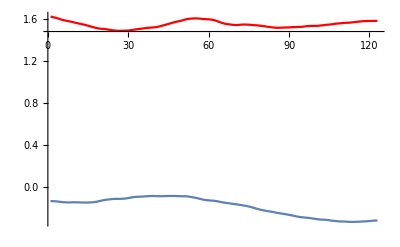

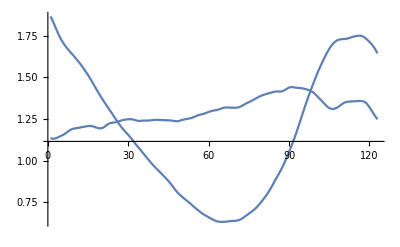

85.9437

5.72958

```mathematica
BODl=ListLinePlot[BOD[[StartLC;;EndLC,1]]];
BODv=ListLinePlot[BOD[[StartLC;;EndLC,2]],PlotStyle->Red];
BODh=ListLinePlot[BOD[[StartLC;;EndLC,3]]];
BODplot=Show[BODv,BODh,PlotRange->All]

FEMl=ListLinePlot[FEM[[StartLC;;EndLC,1]]];
FEMv=ListLinePlot[FEM[[StartLC;;EndLC,2]]];
FEMh=ListLinePlot[FEM[[StartLC;;EndLC,3]]];
FEMplot=Show[FEMv,FEMh,PlotRange->All]

TIBl=ListLinePlot[TIB[[StartLC;;EndLC,1]]];
TIBv=ListLinePlot[TIB[[StartLC;;EndLC,2]]];
TIBh=ListLinePlot[TIB[[StartLC;;EndLC,3]]];
TIBplot=Show[TIBv,TIBh,PlotRange->All];

TARl=ListLinePlot[TAR[[StartLC;;EndLC,1]]];
TARv=ListLinePlot[TAR[[StartLC;;EndLC,2]]];
TARh=ListLinePlot[TAR[[StartLC;;EndLC,3]]];
TARplot=Show[TARv,TARh,PlotRange->All];
1.5/Degree
0.1/Degree
```

```mathematica
(*********************)
```

```mathematica
FEMDATAv=FEM[[StartLC;;EndLC,2]];
FEMDATAh=FEM[[StartLC;;EndLC,3]];

TIBDATAv=TIB[[StartLC;;EndLC,2]];
TIBDATAh=TIB[[StartLC;;EndLC,3]];

TARDATAv=TAR[[StartLC;;EndLC,2]];
TARDATAh=TAR[[StartLC;;EndLC,3]];
```

```mathematica
(*export*)
```

```mathematica
dataDirectory="YOUR DIRECTORY FOR EXPORTED POLAR COORDINATES";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

Export[StringJoin[AnimalDataTrialforexporting,"_","FemurVertical.xlsx"],FEMDATAv];
Export[StringJoin[AnimalDataTrialforexporting,"_","FemurHorizontal.xlsx"],FEMDATAh];

Export[StringJoin[AnimalDataTrialforexporting,"_","TibfibVertical.xlsx"],TIBDATAv];
Export[StringJoin[AnimalDataTrialforexporting,"_","TibfibHorizontal.xlsx"],TIBDATAh];

Export[StringJoin[AnimalDataTrialforexporting,"_","TarsalsVertical.xlsx"],TARDATAv];
Export[StringJoin[AnimalDataTrialforexporting,"_","TarsalsHorizontal.xlsx"],TARDATAh];

Print["EXPORTED"]
```

EXPORTED